```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
datafull=Import["../data/ccm1_data_modified.csv",HeaderLines->1];
```

```mathematica
Dimensions@datafull
```

{459203,16}

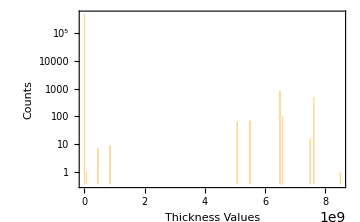
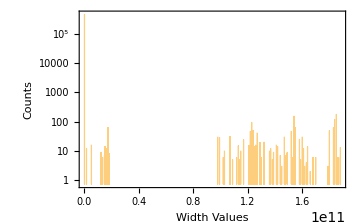

```mathematica
{Histogram[datafull[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
datafullnoNA=datafull/."NA"->0.;
```

```mathematica
thickpostobeconverted=Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(7<#&)];
```

```mathematica
Length@thickpostobeconverted
```

1561

```mathematica
datafullnoNA[[Flatten@thickpostobeconverted,9]]/=10^8;
datafullnoNA[[Flatten@thickpostobeconverted,10]]/=10^8;
```

```mathematica
Counts@datafullnoNA[[Flatten@thickpostobeconverted,10]]
Counts@datafullnoNA[[Flatten@thickpostobeconverted,9]]
```

<|65.8→100,65.→811,0.751→1,76.2→482,50.8→65,75.→16,55.→69,85.→1,4.54→7,8.5→9|>

<|1850.→174,1230.→89,1840.→119,1540.→149,1600.→30,1530.→6,1610.→12,161.→12,1550.→62,0.→3,1580.→12,1830.→63,1630.→4,1070.→31,1240.→49,1270.→41,1250.→14,1410.→16,1880.→13,1210.→15,1490.→9,1380.→5,993.→28,0.0102→11,1150.→10,1620.→3,1800.→49,1520.→38,169.→5,134.→6,1480.→7,148.→7,1640.→14,1220.→47,1790.→3,1420.→14,1290.→19,1120.→6,1470.→30,157.→7,1450.→3,173.→62,1700.→6,1090.→5,1370.→12,127.→5,980.→30,15.4→12,1300.→6,1870.→6,1320.→20,1590.→5,1130.→15,1360.→10,165.→12,1440.→7,1860.→6,1170.→24,1030.→10,1020.→6,182.→8,1140.→5,1260.→16,152.→14,124.→9,1390.→9,1680.→6|>

```mathematica
datafullnoNA[[All,10]]=datafullnoNA[[All,10]]/. {0.751->75.1,4.54->45.4,8.5->85.};
datafullnoNA[[All,9]]=datafullnoNA[[All,9]]/. {161.->1610.,0.0102->1020.,169.->1690.,134.->1340.,148.->1480.,157.->1570.,173.->1730.,127.->1270.,15.4->1540.,165.->1650.,182.->1820.,152.->1520.,124.->1240.};
```

```mathematica
datafullnoNA[[Flatten[Position[datafullnoNA[[All,11]],_?Negative],1],11]]*=-1;
```

```mathematica
RealDigits@1.66*^10
```

{{1,6,6,0,0,0,0,0,0,0,0,0,0,0,0,0},11}

```mathematica
datafullnoNA[[Flatten@thickpostobeconverted[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpostobeconverted,11]]][[All,2]],_?(10≤#≤11&)]]],11]]/=10^6;
datafullnoNA[[Flatten@thickpostobeconverted[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpostobeconverted,11]]][[All,2]],_?(#==9&)]]],11]]/=10^5;
datafullnoNA[[Flatten@thickpostobeconverted[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpostobeconverted,11]]][[All,2]],_?(#==8&)]]],11]]/=10^4;
datafullnoNA[[Flatten@thickpostobeconverted[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpostobeconverted,11]]][[All,2]],_?(#==7&)]]],11]]/=10^3;
```

```mathematica
datafullnoNA[[Flatten@thickpostobeconverted,11]]
```

```mathematica
Counts@datafullnoNA[[Flatten@thickpostobeconverted,12]]
Counts@datafullnoNA[[Flatten@thickpostobeconverted,11]]
```

<|29000.→5,24000.→16,17000.→21,18000.→40,22000.→21,21000.→68,2.01×10^9→48,2.74×10^9→6,28000.→11,25000.→5,35000.→17,26000.→20,2.65×10^9→7,31000.→16,4.33×10^8→12,4.08×10^9→4,27000.→21,4.54×10^9→15,2.29×10^9→17,2.38×10^9→6,3.25×10^9→6,3.18×10^6→7,3.14×10^9→20,3.11×10^9→14,3.66×10^9→7,23000.→11,34000.→16,3.87×10^9→34,19000.→14,4.69×10^9→24,3.81×10^9→20,30000.→5,1.97×10^9→1,2.22×10^9→1,20000.→5,3.72×10^9→10,2.67×10^12→6,2.18×10^8→7,1.87×10^12→7,2.17×10^9→7,2.02×10^12→7,4.6×10^9→6,3.17×10^12→3,2.66×10^12→11,2.6×10^12→22,2.99×10^12→6,2.96×10^9→20,3.38×10^8→5,1.75×10^12→12,3.41×10^9→25,2.62×10^9→7,3.32×10^12→9,1.9×10^12→20,4.11×10^9→10,3.05×10^9→7,3.29×10^9→6,3.99×10^9→13,3.69×10^9→7,3.08×10^9→7,2.99×10^9→6,3.54×10^9→7,1.91×10^11→62,3.07×10^12→38,1.74×10^12→28,1.94×10^12→6,2.03×10^12→7,2.27×10^12→4,2.19×10^12→5,3.93×10^9→15,2.11×10^12→6,2.69×10^12→9,2.61×10^12→19,2.54×10^12→18,2.32×10^12→5,1.77×10^12→5,2.76×10^12→5,2.1×10^12→25,2.16×10^12→10,1.8×10^12→20,2.14×10^12→12,3.63×10^9→5,2.89×10^11→6,3.2×10^9→11,4.15×10^9→7,2.19×10^9→5,3.44×10^9→8,3.26×10^9→14,3.51×10^9→14,2.93×10^9→6,2.31×10^12→5,2.55×10^12→4,4.72×10^9→7,3.57×10^9→13,2.46×10^12→5,2.13×10^9→5,2.5×10^9→7,2.52×10^12→19,3.84×10^9→7,3.78×10^9→7,3.75×10^9→6,2.68×10^9→4,2.45×10^12→15,3.96×10^9→24,2.24×10^12→10,2.98×10^12→5,1.91×10^6→7,4.05×10^9→15,2.56×10^12→7,2.07×10^12→18,3.01×10^11→23,3.22×10^12→30,3.18×10^12→23,3.06×10^12→3,1.86×10^12→7,2.83×10^9→7,3.39×10^12→5,2.58×10^12→16,1.06×10^11→7,2.13×10^11→7,2.86×10^11→2,1.82×10^12→7,2.32×10^9→7,2.48×10^12→12,2.61×10^11→6,2.97×10^12→5,3.48×10^12→9,2.85×10^12→6|>

<|4550.→5,1530.→18,2250.→11,12800.→6,1000.→19,2050.→12,1150.→48,4050.→6,2550.→10,3050.→6,0→177,1250.→13,5470.→13,7530.→7,1650.→6,160.→11,2650.→7,176.→4,3530.→3,2850.→4,2950.→4,1550.→11,0.147→6,2470.→13,9530.→12,5300.→13,5530.→27,2530.→5,4150.→6,16000.→41,1847→29,5850.→12,2000.→10,1.5→22,3000.→23,9000.→18,16500.→5,7000.→19,1347→14,3200.→11,16600.→5,15700.→5,8490.→5,8540.→5,8470.→5,86.5→3,8480.→8,9470.→7,85.→7,15100.→13,8530.→5,8440.→7,1350.→8,2200.→53,0.5→11,84.5→12,15200.→14,8000.→28,1120.→7,1300.→23,1900.→19,1800.→7,14900.→45,1750.→7,8380.→7,1200.→21,15800.→3,8190.→7,14400.→28,1420.→10,2560.→4,1610.→14,6100.→33,2360.→4,4460.→8,14100.→18,2100.→52,1470.→4,2400.→14,3730.→4,2.→39,2.5→9,2800.→18,2900.→6,2300.→14,4600.→4,8760.→3,2700.→5,3600.→15,1653→7,6000.→13,3400.→12,2600.→47,5050.→4,8770.→5,3.→11,14500.→16,4000.→6,3300.→8,14700.→8,67.→1,14600.→11,1600.→8,2380.→3,1700.→6,4200.→4,1490.→10,15400.→15,1.→6,4400.→4,14800.→6,15000.→4,1100.→6|>

```mathematica
Position[datafullnoNA[[All,11]],3400.]
datafullnoNA[[Flatten@Position[datafullnoNA[[All,11]],3400.],13]]
```

{{263131},{263132},{263133},{263134},{263135},{263136},{263137},{267160},{267161},{267162},{267163},{267164}}

{17107961,17107961,17107961,17107961,17107961,17107961,17107961,17121161,17121161,17121161,17121161,17121161}

```mathematica
ReverseSortBy[Last@*Total]@%196;
```

Last::normal: Nonatomic expression expected at position 1 in Last[5].

Last::normal: Nonatomic expression expected at position 1 in Last[11].

General::stop: Further output of Last::normal will be suppressed during this calculation.

```mathematica
KeySort@%219
```

<|0→177,0.147→6,0.5→11,1.→6,1.5→22,2.→39,2.5→9,3.→11,67.→1,84.5→12,85.→7,86.5→3,160.→11,176.→4,1000.→19,1100.→6,1120.→7,1150.→48,1200.→21,1250.→13,1300.→23,1347→14,1350.→8,1420.→10,1470.→4,1490.→10,1530.→18,1550.→11,1600.→8,1610.→14,1650.→6,1653→7,1700.→6,1750.→7,1800.→7,1847→29,1900.→19,2000.→10,2050.→12,2100.→52,2200.→53,2250.→11,2300.→14,2360.→4,2380.→3,2400.→14,2470.→13,2530.→5,2550.→10,2560.→4,2600.→47,2650.→7,2700.→5,2800.→18,2850.→4,2900.→6,2950.→4,3000.→23,3050.→6,3200.→11,3300.→8,3400.→12,3530.→3,3600.→15,3730.→4,4000.→6,4050.→6,4150.→6,4200.→4,4400.→4,4460.→8,4550.→5,4600.→4,5050.→4,5300.→13,5470.→13,5530.→27,5850.→12,6000.→13,6100.→33,7000.→19,7530.→7,8000.→28,8190.→7,8380.→7,8440.→7,8470.→5,8480.→8,8490.→5,8530.→5,8540.→5,8760.→3,8770.→5,9000.→18,9470.→7,9530.→12,12800.→6,14100.→18,14400.→28,14500.→16,14600.→11,14700.→8,14800.→6,14900.→45,15000.→4,15100.→13,15200.→14,15400.→15,15700.→5,15800.→3,16000.→41,16500.→5,16600.→5|>

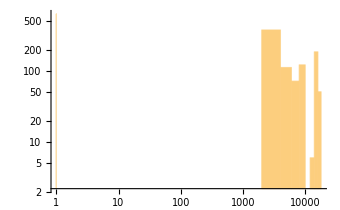
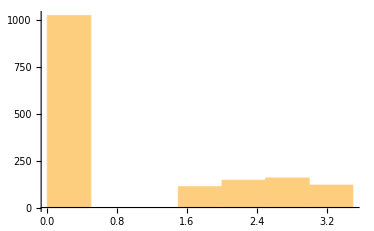

```mathematica
{Histogram[datafullnoNA[[Flatten@thickpostobeconverted,11]],ScalingFunctions->{"Log","Log"}],Histogram@datafullnoNA[[Flatten@thickpostobeconverted,12]]}
```

```mathematica
7.55*10^(-6)*65*1540*27300
7.85*10^(-6)*65.8*1540*2100
7.85*10^(-6)*85*2000*20000
7.42*10^(-6)*76.2*185*32600
```

20632.1

1670.46

26690.

3409.95

```mathematica
densitycheck[data_,pos_]:=data[[Flatten@pos,11]]/(data[[Flatten@pos,9]]*data[[Flatten@pos,10]]*data[[Flatten@pos,12]])
```

```mathematica
densitycheck[datafullnoNA,thickpostobeconverted];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
%140;
```

```mathematica
ReverseSortBy[Last@*Total]@Counts@%222
```

Last::normal: Nonatomic expression expected at position 1 in Last[5].

General::stop: Further output of Last::normal will be suppressed during this calculation.

<|0.→177,6.70455×10^-13→28,4.69274×10^-12→24,4.6636×10^-12→24,2.84012×10^-13→20,1.8315×10^-14→20,4.19043×10^-12→18,1.07185×10^-14→15,2.46905×10^-12→14,6.93735×10^-13→14,6.55694×10^-14→14,7.6947×10^-15→14,4.1806×10^-6→12,5.22203×10^-12→12,3.9255×10^-14→12,8.84224×10^-18→12,1.52625×10^-14→10,7.05152×10^-15→10,5.80484×10^-15→10,3.95334×10^-15→10,1.08204×10^-6→8,1.91045×10^-11→8,1.04044×10^-11→8,9.6833×10^-12→8,8.22355×10^-12→8,3.45282×10^-12→8,2.13242×10^-12→8,8.55327×10^-14→8,7.18329×10^-14→8,1.83382×10^-14→8,1.24168×10^-14→8,8.45309×10^-15→8,7.79525×10^-15→8,3.58213×10^-6→7,2.46191×10^-6→7,1.26064×10^-6→7,6.02093×10^-8→7,7.2479×10^-10→7,6.91677×10^-11→7,6.29592×10^-11→7,2.35518×10^-11→7,1.93231×10^-11→7,1.91598×10^-11→7,1.88628×10^-11→7,1.86681×10^-11→7,1.81216×10^-11→7,1.759×10^-11→7,1.58628×10^-11→7,1.53611×10^-11→7,1.34392×10^-11→7,1.18534×10^-11→7,9.77578×10^-12→7,7.39835×10^-12→7,7.2756×10^-12→7,6.72679×10^-12→7,6.67271×10^-12→7,6.309×10^-12→7,5.83805×10^-12→7,5.74271×10^-12→7,5.5591×10^-12→7,5.45432×10^-12→7,4.98608×10^-12→7,4.91767×10^-12→7,4.11464×10^-12→7,3.87501×10^-12→7,2.62585×10^-12→7,2.53024×10^-12→7,2.38444×10^-12→7,2.33211×10^-12→7,1.47048×10^-12→7,1.96117×10^-13→7,1.23548×10^-13→7,8.44942×10^-14→7,8.16882×10^-14→7,7.12118×10^-14→7,4.61481×10^-14→7,2.91538×10^-14→7,1.02678×10^-14→7,8.12827×10^-15→7,4.59407×10^-15→7,4.49677×10^-15→7,1.48903×10^-17→7,7.5189×10^-6→6,5.87346×10^-6→6,4.22396×10^-6→6,3.01659×10^-6→6,2.48388×10^-6→6,2.48372×10^-6→6,2.47029×10^-6→6,1.43329×10^-6→6,9.90621×10^-7→6,9.89583×10^-7→6,9.75215×10^-7→6,7.02062×10^-7→6,5.94643×10^-7→6,7.13572×10^-10→6,6.72702×10^-11→6,3.43727×10^-11→6,2.84046×10^-11→6,2.67485×10^-11→6,1.91722×10^-11→6,1.89252×10^-11→6,1.56501×10^-11→6,1.45363×10^-11→6,1.32723×10^-11→6,1.26782×10^-11→6,6.44656×10^-12→6,5.03428×10^-12→6,3.98239×10^-12→6,3.44445×10^-12→6,2.33845×10^-12→6,4.90952×10^-13→6,2.03865×10^-13→6,8.3272×10^-14→6,7.42648×10^-14→6,7.19696×10^-14→6,6.5822×10^-14→6,2.84555×10^-14→6,1.53353×10^-14→6,1.35379×10^-14→6,1.23047×10^-14→6,1.1363×10^-14→6,1.07161×10^-14→6,9.07788×10^-15→6,8.22707×10^-15→6,4.17711×10^-15→6,4.07457×10^-15→6,2.96453×10^-15→6,8.65593×10^-17→6,2.34207×10^-18→6,9.08817×10^-6→5,7.82751×10^-6→5,7.5528×10^-6→5,7.43218×10^-6→5,7.18329×10^-6→5,5.14536×10^-6→5,4.12105×10^-6→5,3.8734×10^-6→5,3.53554×10^-6→5,3.36022×10^-6→5,3.34055×10^-6→5,1.52229×10^-6→5,1.28889×10^-6→5,1.2758×10^-6→5,1.16093×10^-6→5,1.15091×10^-6→5,1.1391×10^-6→5,1.10663×10^-6→5,8.62363×10^-7→5,7.97373×10^-7→5,7.18041×10^-7→5,4.10147×10^-7→5,7.32192×10^-8→5,2.27583×10^-10→5,3.67576×10^-11→5,2.72835×10^-11→5,1.04384×10^-11→5,2.61755×10^-13→5,7.52464×10^-14→5,6.72607×10^-14→5,5.93155×10^-14→5,5.28583×10^-14→5,1.47088×10^-14→5,1.332×10^-14→5,1.16604×10^-14→5,1.08929×10^-14→5,1.06403×10^-14→5,1.0543×10^-14→5,1.00356×10^-14→5,9.38659×10^-15→5,9.08183×10^-15→5,4.92812×10^-15→5,1.18929×10^-17→5,9.4061×10^-18→5,8.50261×10^-18→5,3.6482×10^-18→5,3.92048×10^-6→4,6.59127×10^-8→4,9.2663×10^-11→4,8.50307×10^-11→4,5.29925×10^-11→4,3.3648×10^-11→4,1.21709×10^-11→4,5.18508×10^-12→4,1.31056×10^-13→4,3.6482×10^-14→4,3.12568×10^-14→4,2.44379×10^-14→4,1.36027×10^-14→4,7.94072×10^-15→4,7.12715×10^-15→4,6.57034×10^-15→4,6.4693×10^-15→4,7.9384×10^-18→4,ComplexInfinity→3,2.42855×10^-6→3,9.45662×10^-7→3,7.84929×10^-7→3,6.07367×10^-7→3,4.42023×10^-7→3,4.56686×10^-8→3,2.34704×10^-8→3,3.84407×10^-11→3,2.61411×10^-11→3,6.33435×10^-13→3,9.80804×10^-15→3,7.77295×10^-15→3,4.15109×10^-6→2,6.68776×10^-14→2,1.7629×10^-14→2,1.08452×10^-16→2,1.15306×10^-17→2,3.93022×10^-7→1,3.17876×10^-11→1,3.33957×10^-13→1,4.76093×10^-14→1,2.78255×10^-16→1|>

```mathematica
nonzerothicknesspos=Position[datafull[[All,10]],x_/;!TrueQ[x==0],{1},Heads->False];
nonNAthicknesspos=Position[datafull[[All,10]],x_/;!TrueQ[x=="NA"],{1},Heads->False];
nonzeroandNAthicknessposs=Intersection[nonzerothicknesspos,nonNAthicknesspos];
datafullwiththicknonzero=datafull[[Flatten@nonzeroandNAthicknessposs,All]];
Dimensions@datafullwiththicknonzero;(*zeros are 13% of the whole data*)
```

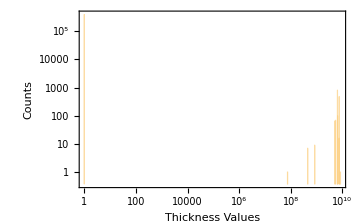
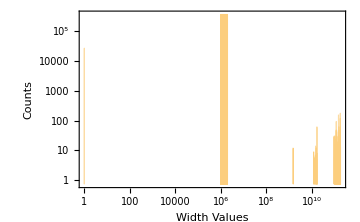
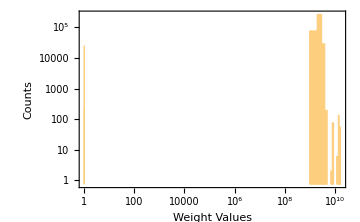
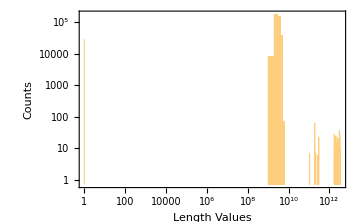

```mathematica
{Histogram[datafullwiththicknonzero[[All,10]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullwiththicknonzero[[All,9]],{10^6},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullwiththicknonzero[[All,11]],{10^9},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium],Histogram[datafullwiththicknonzero[[All,12]],{10^9},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium]}
```

```mathematica
N@25000/(85*800*20000)
```

0.0000183824

```mathematica
datafullnoNA=datafull/."NA"->0;
```

```mathematica
datafullnoNA[[All,9]]/=1000;
datafullnoNA[[All,12]]/=1000;
datafullnoNA[[All,11]]/=1000;
```

```mathematica
datafullnoNA[[Flatten[Position[datafullnoNA[[All,11]],_?Negative],1],11]]*=-1;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,9]]][[All,2]],_?(6<#&)],1],9]]/=10^5;
```

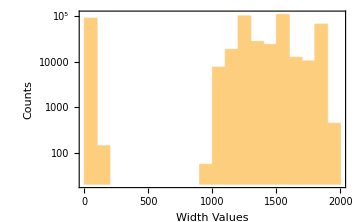

```mathematica
Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(7<#&)],1],10]]/=10^8;
```

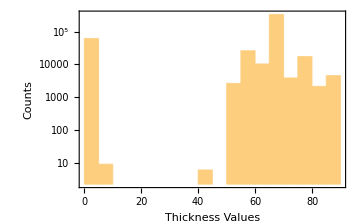

```mathematica
Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium]
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(8≤#&)],1],12]]/=10^6;
```

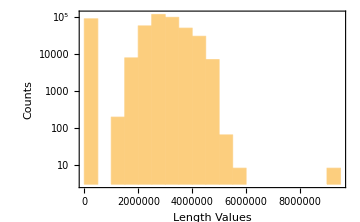

```mathematica
Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium]
```

```mathematica
Length@Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(#==6&)]
Length@Position[RealDigits[datafullnoNA[[All,11]]][[All,2]],_?(#==6&)]
```

25471

39742

```mathematica
Length@datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(2<#&)],1],10]]
Length@datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,9]]][[All,2]],_?(5≤#&)],1],9]]
Length@datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,11]]][[All,2]],_?(8<#&)],1],11]]
Length@datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(8<#&)],1],12]]
```

0

0

0

«1 more identical outputs»

```mathematica
c=Flatten[Position[RealDigits[datafullnoNA[[All,12]]][[All,2]],_?(8<#&)],1];
b=Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1];
a=Flatten[Position[RealDigits[datafullnoNA[[All,9]]][[All,2]],_?(5≤#&)],1];
```

```mathematica
Count[Table[MemberQ[a,i],{i,c}],True]
```

0

```mathematica
row=datafullnoNA[[37,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[8396,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
```

{1520.,66.,2.07×10^6,274000.}

0.0000753065

{1520.,66.,2.08×10^6,2.75×10^6}

7.53951×10^-6

```mathematica
row=datafullnoNA[[15,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
```

{1220.,65.,207000.,3.42×10^6}

7.63257×10^-7

```mathematica
7.694697349869764*^-24*10^5*10^8*10^5
```

7.6947×10^-6

```mathematica
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.973733583489682*^-19]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.940717777361331*^-25]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.694697349869764*^-24]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.275597826778928*^-21]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.135721421435708*^-23]]]
Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1][[Flatten@Position[table,7.051518679425656*^-22]]]
```

{}

{}

{}

«3 more identical outputs»

```mathematica
rowtable=datafullnoNA[[Flatten[Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(5≤#&)],1],9;;12]];
table=Table[N@i[[3]]/(i[[1]]*i[[2]]*i[[4]]),{i,rowtable}];
Length@table
table
```

0

{}

```mathematica
densities=datafull[[All,11]]/(datafull[[All,9]]*datafull[[All,10]]*datafull[[All,12]]);
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
densitieswithconvertedvalues=datafullnoNA[[All,11]]/(datafullnoNA[[All,9]]*datafullnoNA[[All,10]]*datafullnoNA[[All,12]]);
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Counts@densitieswithconvertedvalues
```

<|7.58167×10^-6→110,7.62861×10^-6→39,7.63257×10^-6→192,7.59272×10^-6→148,7.54014×10^-6→75,7.53065×10^-6→40,ComplexInfinity→50862,7.55846×10^-6→97,7.62036×10^-6→47,7.63562×10^-6→187,7.62979×10^-6→43,7.63826×10^-6→140,14776,7.48739×10^-6→7,7.48094×10^-6→5,7.47589×10^-6→18,7.48938×10^-6→6,7.46132×10^-6→7,7.36805×10^-6→7,7.46339×10^-6→12,7.4496×10^-6→11,7.42502×10^-6→32,7.49466×10^-6→6,7.40059×10^-6→4,7.46356×10^-6→4|>
 |  |  |  |

```mathematica
densitieswithconvertedvaluesallreal=densitieswithconvertedvalues/.{Indeterminate->0,ComplexInfinity->0};
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-6&)];
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)],1],12]]*=10;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-6&)],1],11]]*=10;
```

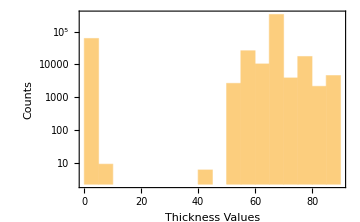
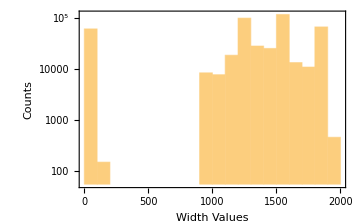
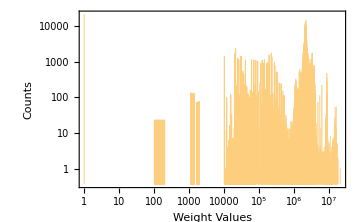
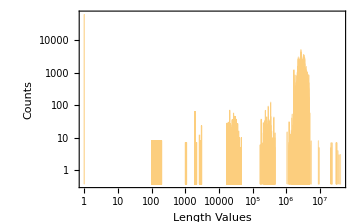

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Automatic,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Automatic,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],{10^2},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],{10^2},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium]}
```

```mathematica
Counts@densitieswithconvertedvalues
```

<|7.58167×10^-6→102,7.62861×10^-6→39,7.63257×10^-7→8,7.59272×10^-6→134,7.54014×10^-6→75,0.0000753065→8,ComplexInfinity→50862,7.55846×10^-6→97,7.63257×10^-6→184,7.62036×10^-6→47,7.63562×10^-6→181,7.62979×10^-6→43,17557,7.48094×10^-6→5,7.47589×10^-6→18,7.48938×10^-6→6,7.46132×10^-6→7,7.36805×10^-6→7,7.46339×10^-6→12,7.4496×10^-6→11,7.42502×10^-6→32,7.44009×10^-7→6,7.49466×10^-6→6,7.40059×10^-6→4,0.0000746356→4|>
 |  |  |  |

```mathematica
RealDigits@7.558461594214153*^-6
RealDigits@0.00007530646456885412
```

{{7,5,5,8,4,6,1,5,9,4,2,1,4,1,5,3},-5}

{{7,5,3,0,6,4,6,4,5,6,8,8,5,4,1,2},-4}

```mathematica
densitieswithconvertedvalues=datafullnoNA[[All,11]]/(datafullnoNA[[All,9]]*datafullnoNA[[All,10]]*datafullnoNA[[All,12]]);
densitieswithconvertedvaluesallreal=densitieswithconvertedvalues/.{Indeterminate->0,ComplexInfinity->0};
Length@Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-5&)]
Length@densitieswithconvertedvaluesallreal[[Flatten@Position[densitieswithconvertedvalues,_?(10^(-6)<#<10^(-5)&)]]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

397666

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

397666

```mathematica
RealDigits@7.566204287515763*^-11
RealDigits@7.429082120934902*^-8
RealDigits@0.7597403069496246
RealDigits@0.0007618610082215906
RealDigits@0.00007566204287515763
RealDigits@0.007827510140183591
RealDigits@0.07229982293920913
RealDigits@7.938398031277288*^-10
RealDigits@7.940717777361331*^-12
RealDigits@8.655928986758592*^-9
```

{{7,5,6,6,2,0,4,2,8,7,5,1,5,7,6,3},-10}

{{7,4,2,9,0,8,2,1,2,0,9,3,4,9,0,2},-7}

{{7,5,9,7,4,0,3,0,6,9,4,9,6,2,4,6},0}

{{7,6,1,8,6,1,0,0,8,2,2,1,5,9,0,6},-3}

{{7,5,6,6,2,0,4,2,8,7,5,1,5,7,6,3},-4}

{{7,8,2,7,5,1,0,1,4,0,1,8,3,5,9,2},-2}

{{7,2,2,9,9,8,2,2,9,3,9,2,0,9,1,3},-1}

{{7,9,3,8,3,9,8,0,3,1,2,7,7,2,8,8},-9}

{{7,9,4,0,7,1,7,7,7,7,3,6,1,3,3,1},-11}

{{8,6,5,5,9,2,8,9,8,6,7,5,8,5,9,3},-8}

```mathematica
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-10&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-7&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==0&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-3&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)];
```

```mathematica
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-2&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-1&)];
```

```mathematica
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-9&)];
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-11&)];
```

```mathematica
Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-8&)];
```

```mathematica
row=datafullnoNA[[1996,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[7352,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[163,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[73901,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[1996,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[156302,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[12436,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[45082,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[152187,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
row=datafullnoNA[[249691,9;;12]]
N@row[[3]]/(row[[1]]*row[[2]]*row[[4]])
```

{1290.,87.,20.5,2.41×10^6}

7.57928×10^-11

{1530.,65.,13750,1.83×10^6}

7.55521×10^-8

{1220.,65.,2.12×10^6,35.}

0.763826

{1860.,65.,2.1×10^6,22750}

0.000763504

{1290.,87.,20.5,2.41×10^6}

7.57928×10^-11

{1840.,65.,1.49×10^7,19000.}

0.00655694

{1390.,65.,203000.,29.5}

0.0761633

{1540.,65.,1.5,21000.}

7.13572×10^-10

{1210.,65.,1.5,3.87×10^6}

4.92812×10^-12

{1230.,65.,2.,2890.}

8.65593×10^-9

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-10&)],1],11]]*=10^6;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-7&)],1],11]]*=10^2;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==0&)],1],12]]*=10^5;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-3&)],1],12]]*=10^2;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)],1],11]]/=10;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-2&)],1],12]]*=10^3;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-1&)],1],11]]*=10;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-1&)],1],12]]*=10^5;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-9&)],1],11]]*=10^6;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-9&)],1],12]]*=10^2;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-11&)],1],11]]*=10^6;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-8&)],1],11]]*=10^6;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-8&)],1],12]]*=10^3;
```

```mathematica
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-4&)],1],12]]*=10;
datafullnoNA[[Flatten[Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-6&)],1],11]]*=10;
```

```mathematica
Length@Join[Position[densitieswithconvertedvaluesallreal,0],Position[densitieswithconvertedvaluesallreal,0.]]
Length@Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#!=-5&)]
```

61530

62588

```mathematica
densitieswithconvertedvalues=datafullnoNA[[All,11]]/(datafullnoNA[[All,9]]*datafullnoNA[[All,10]]*datafullnoNA[[All,12]]);
densitieswithconvertedvaluesallreal=densitieswithconvertedvalues/.{Indeterminate->0,ComplexInfinity->0};
Length@Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#==-5&)]
Length@densitieswithconvertedvaluesallreal[[Flatten@Position[densitieswithconvertedvalues,_?(10^(-6)<#<10^(-5)&)]]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

397666

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

397666

```mathematica
ReverseSortBy[Last@*Total]@Counts@densitieswithconvertedvaluesallreal[[Complement[Flatten@Position[RealDigits[densitieswithconvertedvaluesallreal][[All,2]],_?(#!=-5&)],Flatten@Join[Position[densitieswithconvertedvaluesallreal,0],Position[densitieswithconvertedvaluesallreal,0.]]]]]
```

Last::normal: Nonatomic expression expected at position 1 in Last[7].

<|1.47048→7|>

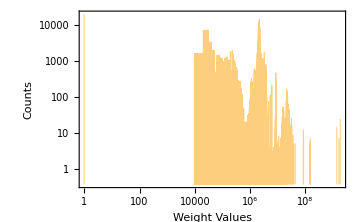
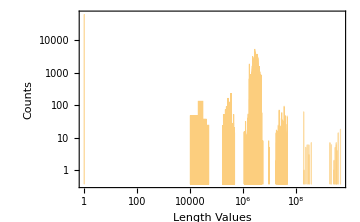
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Automatic,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Automatic,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],{10^4},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],{10^4},ScalingFunctions->{"Log","Log"},PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium]}
```

```mathematica
unacceptabledensitypos=Complement[Complement[Range@Length@densitieswithconvertedvaluesallreal,Flatten@Position[densitieswithconvertedvaluesallreal,_?(7*10^-6<#<8.5*10^-6&)]],Flatten@Join[Position[densitieswithconvertedvaluesallreal,0],Position[densitieswithconvertedvaluesallreal,0.]]];
```

```mathematica
datafullnoNA[[All,9]]=ReplacePart[datafullnoNA[[All,9]],{Partition[unacceptabledensitypos,1]->"NA"}];
datafullnoNA[[All,10]]=ReplacePart[datafullnoNA[[All,10]],{Partition[unacceptabledensitypos,1]->"NA"}];
datafullnoNA[[All,11]]=ReplacePart[datafullnoNA[[All,11]],{Partition[unacceptabledensitypos,1]->"NA"}];
datafullnoNA[[All,12]]=ReplacePart[datafullnoNA[[All,12]],{Partition[unacceptabledensitypos,1]->"NA"}];
```

```mathematica
(* Export["datafull_manipulated.csv",datafullnoNA] *)
```

datafull_manipulated.csv